## ybounds.m _W5R

{r→813.235}

{r→1.53582}

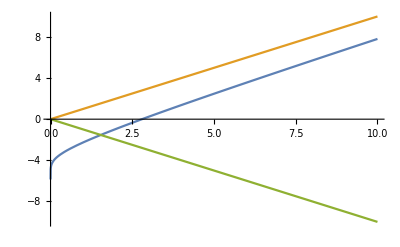

```mathematica
Npart=10000;
A=2*Npart;c=(64(√2)/(210*Npart))^(1/3);d=√(π/2)c; (*√(π/2)c*)
rmax=FindRoot[Log[d/BesselK[0,r]]-r,{r,10^-4}]
rmin=FindRoot[Log[d/BesselK[0,r]]+r,{r,10^-4}]
Plot[{Log[d/BesselK[0,r]],r,-r},{r,0,10}]
```

```mathematica
y=Log[d/BesselK[0,r]];
A=2*Integrate[√(r^2-y^2)(-d/BesselK[0,r])*Abs[BesselK[0,r]],{r,rmin,rmax}]//Simplify
```

$Aborted

```mathematica
Solve[0.04==√(π/2)(64(√2)/(210N))^(1/3),N]//N
```

{{N→13257.9}}

```mathematica
1/(2^3(2/π)^(3/2)210/(64 √3))//N
```

0.129901

```mathematica
d=√(π/2)(64(√2)/(210*10000))^(1/3)//N
```

0.0439425

## Contour2area.m _W6Su

```mathematica
Series[Log[d/BesselK[0,r]],{r,0,3}]//Simplify
```

Log[-d/(EulerGamma+Log[r/2])]-((-1+EulerGamma+Log[r/2]) r^2)/(4 (EulerGamma+Log[r/2]))+O[r]^4